```mathematica
filename="/Users/martinrypdal/Dropbox/FRIPRO/FortranCode/EBM/output/timesteps-output2.nc";
Import[filename];
temp=Import[filename,{"Datasets","temperature"}];
lat=Import[filename,{"Datasets","latitude"}];
lon=Import[filename,{"Datasets","longitude"}];
```

```mathematica
temp2=Drop[Map[Mean[#]&,Partition[Drop[temp,37],4]],-12];
```

```mathematica
Dimensions[temp2]
```

{1166,1,65,128}

```mathematica
Length[temp2]
```

1166

```mathematica
positions=Flatten[Table[GeoPosition[{lat[[i]],lon[[j]]}],{i,1, Length[lat]},{j,1,Length[lon]}]];
M={};
Monitor[
Do[
PL1=GeoContourPlot[positions->Flatten[temp2[[teller,1]]],Contours->{-20,-15,-10,-5,0,5,10},ContourLabels->All,ContourStyle->Thick,PlotLegends->Automatic,GeoProjection->{"Orthographic","Centering"->GeoPosition[{90,0}]},GeoRange->"World"];
PL2=GeoDensityPlot[positions->Flatten[temp2[[teller,1]]], ColorFunction->"TemperatureMap",PlotRange->All,GeoProjection->{"Orthographic","Centering"->GeoPosition[{90,0}]},GeoRange->"World"];
M=Append[M,Rasterize[Show[PL1,PL2]]];
,{teller,1,Length[temp2]}];
,teller];
```

```mathematica
Export["/Users/martinrypdal/Dropbox/FRIPRO/FortranCode/animation.gif",M]
```

/Users/martinrypdal/Dropbox/FRIPRO/FortranCode/animation.gif

```mathematica
12*95
```

1140

```mathematica
ListAnimate[M]
```

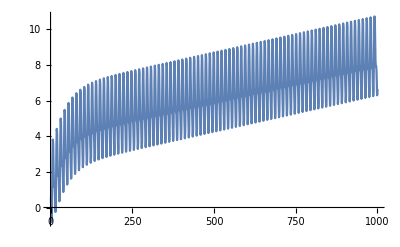

```mathematica
ListPlot[Table[Mean[Flatten[temp2[[i,1]]]],{i,1,1000}], Joined->True]
```